```mathematica
f[x_,μ_:0,σ_:1]:=1/(2 √σ)ⅇ^(-1/2((x-μ)/σ)^2)
```

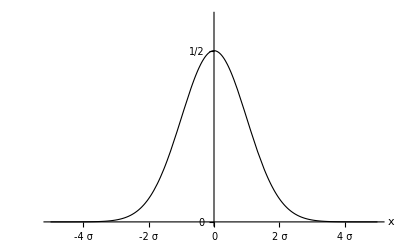

```mathematica
Plot[f[x],{x,-5,5},
PlotRange->{0,6/10},
Ticks->{Table[{i,i"σ"},{i,-4,4,2}],{0,1/2}},
AxesLabel->{x,None},
AxesStyle->Directive[Thickness->0.002, RGBColor[{0.2,0.2,0.2}]],
LabelStyle->Directive[Bold,Medium],
PlotStyle -> Directive[Black, Thickness[0.002]],
ImageSize->600
]
```

```mathematica
Histogram[RandomReal[NormalDistribution[0,1],10^5]]
```

-Graphics-